# q q̄→μ μ in EW theory (SM ): GENERIC CHARGES

mass leptons MM!=0, box calculation

Confronto con:
- EW_MM_Larin per d=4 -> OK
-Nar per d=4 (box photons and born Z)->OK

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
(*Neglect[MM] = Neglect[MM2] = 0;*)
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
(*SetOptions[CalcFeynAmp,PaVeReduce->True];*)
(*SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];*)
```

## SM: Feynman rules and diagrams

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2};
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3};
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3};
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3};
MASSES={MU->0,MU2->0(*,MM->0,MM2->0,*),MD->0,MD2->0,S+T+U->2 MM2}
```

{MU→0,MU2→0,MD→0,MD2→0,S+T+U→2 MM2}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

## Vertices

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

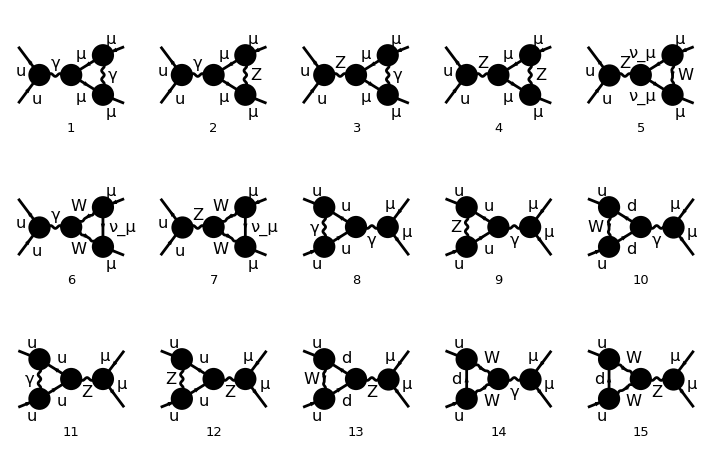

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
```

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

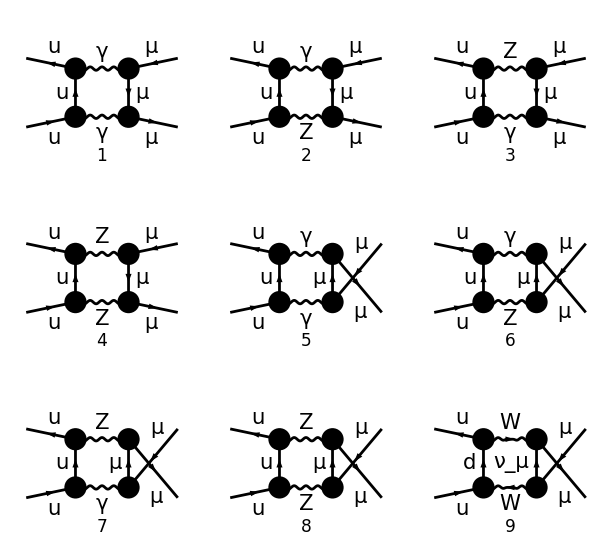

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
```

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

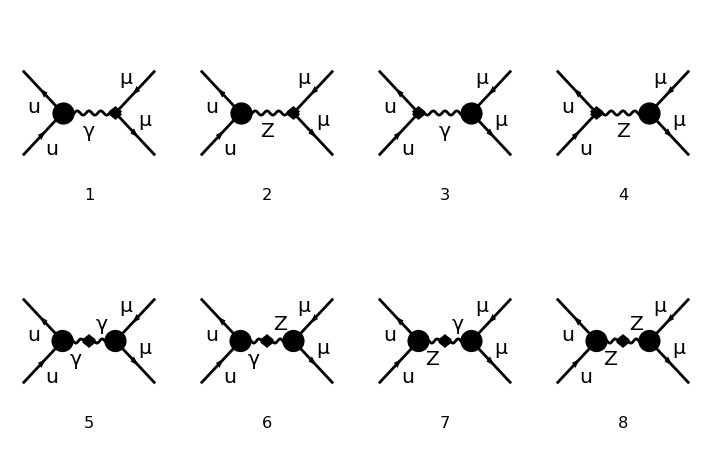

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
```

## BOX

ampiezzabox . ampiezzaborn*

#### Classificazione

```mathematica
(*in input mettere box1*)
boxtable[box_]:=Module[{b1,b2,b3,samediag,b4,tden,uden,boxcl0,boxcl1},

(*primo metodo: topologie*)
b1=Table[
Which[MemberQ[Part[box,{i}][[1,1]],Topology==1,Infinity],T,
MemberQ[Part[box,{i}][[1,1]],Topology==2,Infinity],U,
True,Print["not identified"]],(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box1]}];

(*secondo metodo*)
(*
tden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,2]]],0];
uden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,1]]],0];


boxcl0=Table[boxcl1[i]=Union[Cases[Part[box,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],
{i,1,Length[box]}];
Print[boxcl0];

b1=Table[
Which[MemberQ[boxcl1[i],tden,Infinity],T,
MemberQ[boxcl1[i],uden,Infinity],U,True,Null](*,
DeleteCases[boxcl1[i],uden|tden,Infinity]*),
{i,1,Length[box1]}];
*)
(*******************)

b2=Table[
Which[b1[[i]]===T,
{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W]},
b1[[i]]===U,

{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W]}
,
True,Print["not identified"]](*identificazione diagrammi t con topology 1 e u con topology 2*)
,(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box]}];
b3=Table[{i,b1[[i]],b2[[i]]},{i,1,Length[box]}];
Print[b3];
samediag=Gather[b3,Last[#1]==Last[#2]&];
b4=Table[{couple[i]==Last[samediag[[i,1]]],bbox[i]=Cases[samediag[[i]],_Integer,{2}]},{i,1,Length[samediag]}];(*couples:diag t , diag u*)


b4
];
```

```mathematica
boxtable[box1]
```

{{1,T,{γ,γ}},{2,T,{γ,Z}},{3,T,{Z,γ}},{4,T,{Z,Z}},{5,U,{γ,γ}},{6,U,{γ,Z}},{7,U,{Z,γ}},{8,U,{Z,Z}},{9,U,{W,W}}}

{{couple[1]=={γ,γ},{1,5}},{couple[2]=={γ,Z},{2,6}},{couple[3]=={Z,γ},{3,7}},{couple[4]=={Z,Z},{4,8}},{couple[5]=={W,W},{9}}}

```mathematica
Table[totbbox[i]={Part[box1,{bbox[i][[1]]}][[1,3]],Part[box1,{bbox[i][[2]]}][[1,3]]},{i,1,4}];
totbbox[5]=Part[box1,{bbox[5][[1]]}][[1,3]];
```

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

### Caso box generico:

METTERE MANUALMENTE: totbbox[i] e 1 per fotone e 2 per z per born diagram

```mathematica
tboxzz=totbbox[2][[1]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
uboxzz=totbbox[3][[2]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
wwbox=totbbox[5]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
```

```mathematica
(*confronto Nar*)
tboxzz=tboxzz/.{Q1->-(Q1-P1)}//.{-P1-P2+K2->-K1,P1+P2-K2->K1}
uboxzz=uboxzz/.{Q1->(Q1-P2)}//.2P2-Q1->Q1//.Q1-K1-K2->-Q1+P1+P2//.PropagatorDenominator[Q1-K1,x_]->PropagatorDenominator[-Q1+K1,x]//.PropagatorDenominator[Q1-P2,x_]->PropagatorDenominator[-Q1+P2,x]
```

1/(16 π^4)ⅈ v̄[p1,0].(-ⅈ EL QUl ga[Lor1].om_--ⅈ EL QUr ga[Lor1].om_+).gs[-(p1)+q1].((ⅈ EL (I3U-QZUl SW2) IndexDelta[Col1,Col2] ga[Lor3].om_-)/(CW SW)-(ⅈ EL QZUr SW IndexDelta[Col1,Col2] ga[Lor3].om_+)/CW).u[p2,0] ū[k2,MM].((ⅈ EL (I3L-QZLl SW2) ga[Lor4].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor4].om_+)/CW).(MM+gs[q1-k1]).(-ⅈ EL QLl ga[Lor2].om_--ⅈ EL QLr ga[Lor2].om_+).v[k1,MM] FeynAmpDenominator[1/(p1-q1)^2,1/(-MZ2+(p1+p2-q1)^2),1/(q1)^2,1/(-MM2+(-(q1)+k1)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

1/(16 π^4)ⅈ v̄[p1,0].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[p2-q1].(-ⅈ EL QUl IndexDelta[Col1,Col2] ga[Lor3].om_--ⅈ EL QUr IndexDelta[Col1,Col2] ga[Lor3].om_+).u[p2,0] ū[k2,MM].((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).(MM+gs[q1-k1]).(-ⅈ EL QLl ga[Lor4].om_--ⅈ EL QLr ga[Lor4].om_+).v[k1,MM] FeynAmpDenominator[1/(p2-q1)^2,1/(-MZ2+(p1+p2-q1)^2),1/(q1)^2,1/(-MM2+(-(q1)+k1)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

```mathematica
tboxzz=tboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
uboxzz=uboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
wwbox=wwbox/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]];
```

```mathematica
(*BORN*)
born=Part[born1,{1}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],
Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}]/.{I->-I,-I->I}
(*colour matrix*)
colourborn=Union[Cases[born,_SumOver|_IndexDelta,Infinity]]
(*born propagators*)
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times;
bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

{CONJ[v̄[p2,0].(ⅈ EL QUl ga[Lorbn1].om_-+ⅈ EL QUr ga[Lorbn1].om_+).u[p1,0]],CONJ[ū[k1,MM].(ⅈ EL QLl ga[Lorbn2].om_-+ⅈ EL QLr ga[Lorbn2].om_+).v[k2,MM]]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

SP[Lorbn1,Lorbn2]/(k1+k2)^2

#### colour:

```mathematica
(*LOOP DIAGRAM*)

colourf[diag_]:=Module[{input2,fermionchain},
diagram=diag;
(*trace closed fermion loop(if any)*)
tr=Cases[diagram,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input2=DeleteCases[diagram,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[sunt,trsunt,sumover,colourborn];

colour
];
```

```mathematica
colourf[tboxzz]
colourf[uboxzz]
colourf[wwbox]
colourf[Part[selfff,{4}]]
```

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

«1 more identical outputs»

#### Propagators

```mathematica
(*box t*)
tnumerat=DeleteCases[tboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)//Simplify
(*box u*)
unumerat=DeleteCases[uboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)//Simplify
bornpropag2
```

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (-MZ2+(p1+p2-q1)^2) (p1-q1)^2 (q1)^2 (-MM2+(q1-k1)^2))

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (-MZ2+(p1+p2-q1)^2) (p2-q1)^2 (q1)^2 (-MM2+(q1-k1)^2))

SP[Lorbn1,Lorbn2]/(k1+k2)^2

```mathematica
tnumerat=tnumerat//.MM2->0
unumerat=unumerat//.MM2->0
```

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (-MZ2+(p1+p2-q1)^2) (p1-q1)^2 (q1)^2 (q1-k1)^2)

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (-MZ2+(p1+p2-q1)^2) (p2-q1)^2 (q1)^2 (q1-k1)^2)

#### Trace

```mathematica
(*  naive anticommuting gamma5 definitions   *)
myTr[a_,b_] := 4 SP[a,b];
myTr[x__] := Module[{lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
		    lista = {x};
                    ultima = lista[[-1]];
		    menouno = Delete[lista,-1];
		    menodue = Table[ Delete[ menouno, i], {i,1,Length[menouno]}];
		    coefficienti = Table[ (-1)^(i+1) SP[ultima,menouno[[i]] ],
                                          {i,1,Length[menouno]}];
		    nuovetracce = Map[ Apply[ myTr, # ] &, menodue];

                    risultato = coefficienti.nuovetracce;
                    risultato
 ] /; FreeQ[{x},G5] ;
```

```mathematica
myTr[G5,G5] = 4;
myTr[z___,-G5]:=-myTr[z,G5];
myTr[s___,MM,u___]:=MM myTr[s,u];
myTr[x_,G5] = 0;
myTr[x_,y_,G5] = 0;
myTr[x_,y_,z_,G5] = 0;
myTr[x__,G5] := 0 /; OddQ[Length[{x}]] && FreeQ[{x},G5] ;
myTr[a___,G5,b___,G5,c___] := (-1)^Length[{b}]*myTr[a,b,c] /; FreeQ[{b},G5] ;
myTr[a___,G5,b__] := (-1)^Length[{b}]*myTr[a,b,G5] /; FreeQ[Union[{a},{b}],G5] ;
myTr[a1_,a2_,a3_,a4_,G5] =- 4 I myEps[a1,a2,a3,a4];
 myTr[x___,a1_,a2_,a3_,a4_,a5_,a6_,G5] := Module[ {lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
  index = Unique[a];
  risultato = myTr[x,a1,a2,a3,a6,G5] SP[a4,a5]-
              myTr[x,a1,a2,a3,a5,G5] SP[a4,a6]+
              myTr[x,a1,a2,a3,a4,G5] SP[a5,a6]+
  I  myTr[x,a1,a2,a3,DiracMatrix[Index[Lorentz,index]]] myEps[a4,a5,a6,Index[Lorentz,index]]; 
  risultato
 ]  /; FreeQ[Union[{x},{a1,a2,a3,a4,a5,a6}],G5] ;
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
SP/:SP[DiracSlash[w_],x_]:=SP[w,x];
SP/:SP[DiracMatrix[w_],x_]:=SP[w,x];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=-Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=-Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
SP/:SP[P1,P1]:=0;
SP/:SP[P2,P2]:=0;
SP/:SP[K2,K2]:=MM2;
SP/:SP[K1,K1]:=MM2;
SP/:SP[P1,P2]:=S/2;
SP/: SP[K1,K2]:=S/2-MM2;
SP/: SP[P1,K1]:=(MM2-T)/2;
SP/: SP[P2,K2]:=(MM2-T)/2; 
SP/:SP[P1,K2]:=(MM2-U)/2; 
SP/:SP[P2,K1]:=(MM2-U)/2;
SP/:SP[Q1,Q1]:=Q1^2;
```

```mathematica
(*PROPRIETÀ MYEPS*)
myEps/:myEps[t___,DiracSlash[w_],x___]:=myEps[t,w,x];
myEps/:myEps[t___,DiracMatrix[w_],x___]:=myEps[t,w,x];
myEps /: myEps[a___,Index[Lorentz,mu_],b___] SP[p_,Index[Lorentz,mu_]] := myEps[a,p,b]; 
myEps[a___,b_,c___,b_,d___] := 0
```

```mathematica
move2[a___,ChiralityProjector[pm_],dm:MM|-MM,b___]:=move2[a,dm,ChiralityProjector[pm],b];
move2[a___,ChiralityProjector[pm_],dm:_DiracMatrix|_DiracSlash,b___]:=move2[a,dm,ChiralityProjector[-pm],b];
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=0/;x≠y;
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=move2[a,ChiralityProjector[x],b]/;x==y;
move2[a___,1,b___]:=move2[a,b];
move2[a___,DiracSlash[-FourMomentum[p__]],b___]:=-move2[a,DiracSlash[FourMomentum[p]],b];
(*NOTA: ANTICOMMUTAZIONE IN D-DIMENSIONI *)
```

```mathematica
trr[s___,MM,u___]:=MM trr[s,u];
trr[s___,-MM,u___]:=-MM trr[s,u];
```

```mathematica
(*calcolo traccia*)
traces[statoi_,statof_]:=Module[{tr0f,tr1i,tr2i,tr3i,tr1f,tr2f,tr3f},

(*trace:*)
traceff4[x___, DiracSpinor[z:K2|P2,w_], DiracSpinor[z:K2|P2,w_],y___]:=traceff4[x,(DiracSlash[z]+w),y];
traceff4[ DiracSpinor[z:K2|P2,w_],x__,DiracSpinor[z:K2|P2,w_]]:=traceff4[(DiracSlash[z]+w),x];
traceff4[x___, DiracSpinor[z:K1|P1,w_], DiracSpinor[z:K1|P1,w_],y___]:=traceff4[x,(DiracSlash[z]-w),y];
traceff4[ DiracSpinor[z:K1|P1,w_],x__,DiracSpinor[z:K1|P1,w_]]:=traceff4[(DiracSlash[z]-w),x];
traceff4[a___,-G5,b___]:=- traceff4[a,G5,b];

chargetot=List[chi,chf]//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL};
(*stato i*)
tr1i=Table[traceff4[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}]//.traceff4->move2;(*sposto proiettori in fondo*)
tr1i=tr1i*chargetot[[1]]//.List->Plus//Simplify;(*prova*)
tr2i=Map[Distribute,1/2 tr1i//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)

tr3i=tr2i//.move2->myTr//Expand;(*espando e calcolo traccia*)
(*tr3i=tr2i//.move2->TR(*//.diractracefeync*)//.TR->myTr//Expand;(*espando e calcolo traccia*)
*)
Print["stato i ",1/2 tr1i//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

(*stato f*)
tr0f=Table[traceff4[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[{Distribute[tr0f[[i]]]},{i,1,Length[tr0f]}],Plus->Sequence,{2},Heads->True]//.traceff4->move2;
tr1f=tr1f*chargetot[[2]]//.List->Plus//Simplify;
tr2f=Map[Distribute,1/2 tr1f//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];
tr3f=tr2f//.move2->trr//.trr->myTr//Expand;
(*tr3f=tr2f//.move2->trr//.trr->TR(*//.diractracefeync*)//.TR->myTr//Expand;*)
Print["stato f ",1/2 tr1f//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

Return[{tr3i,tr3f}]

];
```

```mathematica
tr1i=Table[traceff4[stati[[i]]/.List->Sequence],{i,1,Length[stati]}]//.traceff4->move2;(*sposto proiettori in fondo*)
tr1i=tr1i*chargetot[[1]]//.List->Plus//Simplify;(*prova*)
tr2i=Map[Distribute,1/2 tr1i//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity](*sostituisco om+- con espressioni G5 esplicite*)
```

-1/(CW SW)2 ⅈ Alfa EL π QU^2 (-I3U move2[gs[p1],ga[Lor1],gs[p2],ga[Lor3],gs[p2],ga[Lorbn1]]+2 QU SW2 move2[gs[p1],ga[Lor1],gs[p2],ga[Lor3],gs[p2],ga[Lorbn1]]+I3U move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1]]-2 QU SW2 move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1]]-I3U move2[gs[p1],ga[Lor1],gs[p2],ga[Lor3],gs[p2],ga[Lorbn1],-G5]+QU SW2 move2[gs[p1],ga[Lor1],gs[p2],ga[Lor3],gs[p2],ga[Lorbn1],-G5]+QU SW2 move2[gs[p1],ga[Lor1],gs[p2],ga[Lor3],gs[p2],ga[Lorbn1],G5]+I3U move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],-G5]-QU SW2 move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],-G5]-QU SW2 move2[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1],G5])

```mathematica
tr3id=tr2i//.move2->TR//.diractracefeync//.TR->myTr//Expand;(*espando e calcolo traccia*)
```

```mathematica
tr3i=tr2i//.move2->TR//.TR->myTr//Expand;(*espando e calcolo traccia*)
```

```mathematica
diractracefeync=TR[muu_,nuu_,rhoo_,sigg_,dell_,tauu_,G5]->-4 I myEps[nuu,rhoo,sigg,tauu]SP[dell,muu]-4 I myEps[muu,nuu,rhoo,sigg]SP[dell,tauu]-4 I myEps[dell,nuu,rhoo,sigg]SP[muu,tauu]-4 I myEps[dell,muu,sigg,tauu]SP[nuu,rhoo]+4 I myEps[dell,muu,rhoo,tauu]SP[nuu,sigg]-4 I myEps[dell,muu,nuu,tauu]SP[rhoo,sigg]
```

TR[muu_,nuu_,rhoo_,sigg_,dell_,tauu_,G5]→-4 ⅈ myEps[nuu,rhoo,sigg,tauu] SP[dell,muu]-4 ⅈ myEps[muu,nuu,rhoo,sigg] SP[dell,tauu]-4 ⅈ myEps[dell,nuu,rhoo,sigg] SP[muu,tauu]-4 ⅈ myEps[dell,muu,sigg,tauu] SP[nuu,rhoo]+4 ⅈ myEps[dell,muu,rhoo,tauu] SP[nuu,sigg]-4 ⅈ myEps[dell,muu,nuu,tauu] SP[rhoo,sigg]

```mathematica
TR[a___,m_,b__,m_,c___] := (-1)^Length[{b}] d TR[a,b,c]+Sum[ma={b}; tmp=Delete[ma,i]; 
(-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;Head[m]===DiracMatrix; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P1]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P2]; 
TR[a___,m_,b__,m_,c___] :=(-1)^Length[{b}] MM2 TR[a,b,c]+ Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K1]; 
TR[a___,m_,b__,m_,c___] :=(-1)^Length[{b}] MM2 TR[a,b,c]+ Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K2]; 

TR[]:=1;
TR[s___,MM,u___]:=MM TR[s,u];
TR[s___,-MM,u___]:=-MM TR[s,u];
(*semplification diraslash*)
TR[x___,DiracSlash[-z_],y___]:=-TR[x,DiracSlash[z],y];
(*trd2[x___,DiracSlash[s_],DiracMatrix[t_],DiracSlash[s_],y___]:=2*SP[t,s]*trd2[x,DiracSlash[s],y]-trd2[x,DiracSlash[s],DiracSlash[s],DiracMatrix[t],y];
trd2[x___,DiracSlash[s_],DiracSlash[t_],DiracSlash[s_],y___]:=2*SP[t,s]*trd2[x,DiracSlash[s],y]-trd2[x,DiracSlash[s],DiracSlash[s],DiracSlash[t],y];*)

TR[x___,DiracSlash[P1],DiracSlash[P1],y___]:=0;
TR[x___,DiracSlash[P2],DiracSlash[P2],y___]:=0;
TR[x___,DiracSlash[K1],DiracSlash[K1],y___]:=MM2*TR[x,y];
TR[x___,DiracSlash[K2],DiracSlash[K2],y___]:=MM2*TR[x,y];
TR[a___,DiracMatrix[Index[Lorentz,m_]],DiracMatrix[Index[Lorentz,m_]], b___] := d TR[a,b];
       
TR[a_,b_]= 4 SP[a,b];
```

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[P1,_],Infinity]&],1];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[K1,_],Infinity]&],1];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;

tbi2=Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List;(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times;

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[Distribute[tbf[[i]]//.List->f],{i,1,Length[tbf]}],Plus->Sequence,{2},Heads->True]//.f->move2;
tbf3=DeleteCases[tbf2,0,1]//.move2->List;
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times;

Print["trace closed fermion loop(if any): ",tr];
Return[{stati,statf}]
];
```

```mathematica
genericCHZ={QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr};
sostituzione={SP[Q1,Q1]->Q1^2};
```

```mathematica
boxtt=traces[fermiontrace[tboxzz][[1]],fermiontrace[tboxzz][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i -1/(CW SW)2 ⅈ Alfa EL π QU^2 ((-I3U+QU SW2) move2[gs[p1],ga[Lor1],gs[-(p1)+q1],ga[Lor3],gs[p2],ga[Lorbn1],1-G5]+QU SW2 move2[gs[p1],ga[Lor1],gs[-(p1)+q1],ga[Lor3],gs[p2],ga[Lorbn1],1+G5])

stato f 1/(CW SW)2 ⅈ Alfa EL π QL^2 ((I3L-QL SW2) (move2[MM,ga[Lor4],MM,ga[Lor2],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor4],MM,ga[Lor2],-MM,ga[Lorbn2],1-G5])-QL SW2 (move2[MM,ga[Lor4],MM,ga[Lor2],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor4],MM,ga[Lor2],-MM,ga[Lorbn2],1+G5])-QL SW2 (move2[MM,ga[Lor4],MM,ga[Lor2],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor4],MM,ga[Lor2],gs[k1],ga[Lorbn2],1-G5])+(I3L-QL SW2) (move2[MM,ga[Lor4],MM,ga[Lor2],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor4],MM,ga[Lor2],gs[k1],ga[Lorbn2],1+G5])-QL SW2 (move2[MM,ga[Lor4],gs[q1-k1],ga[Lor2],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor4],gs[q1-k1],ga[Lor2],-MM,ga[Lorbn2],1-G5])+(I3L-QL SW2) (move2[MM,ga[Lor4],gs[q1-k1],ga[Lor2],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor4],gs[q1-k1],ga[Lor2],-MM,ga[Lorbn2],1+G5])+(I3L-QL SW2) (move2[MM,ga[Lor4],gs[q1-k1],ga[Lor2],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor4],gs[q1-k1],ga[Lor2],gs[k1],ga[Lorbn2],1-G5])-QL SW2 (move2[MM,ga[Lor4],gs[q1-k1],ga[Lor2],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor4],gs[q1-k1],ga[Lor2],gs[k1],ga[Lorbn2],1+G5]))

```mathematica
boxuu=traces[fermiontrace[uboxzz][[1]],fermiontrace[uboxzz][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i -1/(CW SW)2 ⅈ Alfa EL π QU^2 ((-I3U+QU SW2) move2[gs[p1],ga[Lor1],gs[p2-q1],ga[Lor3],gs[p2],ga[Lorbn1],1-G5]+QU SW2 move2[gs[p1],ga[Lor1],gs[p2-q1],ga[Lor3],gs[p2],ga[Lorbn1],1+G5])

stato f 1/(CW SW)2 ⅈ Alfa EL π QL^2 ((I3L-QL SW2) (move2[MM,ga[Lor2],MM,ga[Lor4],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor4],-MM,ga[Lorbn2],1-G5])-QL SW2 (move2[MM,ga[Lor2],MM,ga[Lor4],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor4],-MM,ga[Lorbn2],1+G5])-QL SW2 (move2[MM,ga[Lor2],MM,ga[Lor4],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor4],gs[k1],ga[Lorbn2],1-G5])+(I3L-QL SW2) (move2[MM,ga[Lor2],MM,ga[Lor4],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor4],gs[k1],ga[Lorbn2],1+G5])-QL SW2 (move2[MM,ga[Lor2],gs[q1-k1],ga[Lor4],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],gs[q1-k1],ga[Lor4],-MM,ga[Lorbn2],1-G5])+(I3L-QL SW2) (move2[MM,ga[Lor2],gs[q1-k1],ga[Lor4],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],gs[q1-k1],ga[Lor4],-MM,ga[Lorbn2],1+G5])+(I3L-QL SW2) (move2[MM,ga[Lor2],gs[q1-k1],ga[Lor4],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],gs[q1-k1],ga[Lor4],gs[k1],ga[Lorbn2],1-G5])-QL SW2 (move2[MM,ga[Lor2],gs[q1-k1],ga[Lor4],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],gs[q1-k1],ga[Lor4],gs[k1],ga[Lorbn2],1+G5]))

## Semplificazioni/sostituzioni

### box T

```mathematica
boxtt=boxtt//Expand;
```

```mathematica
iep=Select[boxtt[[1]],MemberQ[#,_myEps,Infinity]&];
inep=Select[boxtt[[1]],FreeQ[#,_myEps,Infinity]&];

fep=Select[boxtt[[2]],MemberQ[#,_myEps,Infinity]&];
fnep=Select[boxtt[[2]],FreeQ[#,_myEps,Infinity]&];
```

```mathematica
(*Il fatto che però ci siano solo 3 impulsi indipendenti (per la conserv. p1+p2=k1+k2) rende i termini con myEps nulli perché non ci sono abbastanza quantità per saturare gli indici mantenendo l’antisimmetria.
quindi i prodotti sono solo fra termini con myEps e senza myEps ma non misti.*)
```

```mathematica
D1=1/List@@Select[tnumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&];
```

```mathematica
D2=1/List@@Select[unumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&];
```

```mathematica
intdenT[expr_]:=Module[{t,t1,A1},

dennnt=Sort[Table[If[Head[D1[[i]]]===Power,D1[[i,1]]->Sqrt[dn[i]],D1[[i]]->dn[i]],{i,1,Length[D1]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D1]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];
t=ReplaceAllRestricted[expr,dennnt,{SP}]//Expand;
If[Head[t]===Plus,
t=List@@t;
expon=Table[DENt@@Table[-1*Exponent[t[[j]],dn[i]],{i,1,Length[D1]}],{j,1,Length[t]}],
expon=DENt@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D1]}]];
t1=t*expon//.canden//.K1+K2->Sqrt[S]//.List->Plus;

t1
];


intdenU[expr_]:=Module[{t,t1,A2},

dennnu=Sort[Table[If[Head[D2[[i]]]===Power,D2[[i,1]]->Sqrt[dn[i]],D2[[i]]->dn[i]],{i,1,Length[D2]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D2]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];(*sostituire solo se certa head*)
t=ReplaceAllRestricted[expr,dennnu,{SP}]//Expand;
If[Head[t]===Plus,
t=List@@t;
expon=Table[DENu@@Table[-1*Exponent[t[[j]],dn[i]],{i,1,Length[D2]}],{j,1,Length[t]}],
expon=DENu@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D2]}]];
t1=t*expon//.canden//.K1+K2->Sqrt[S]//.List->Plus;

t1
];
```

```mathematica
intdenT[tnumerat]
intdenU[unumerat]
```

(ⅈ DENt[1,1,1,1] SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4)

(ⅈ DENu[1,1,1,1] SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4)

```mathematica
D1
D2
```

{-MZ2+(p1+p2-q1)^2,(p1-q1)^2,(q1)^2,(q1-k1)^2}

{-MZ2+(p1+p2-q1)^2,(p2-q1)^2,(q1)^2,(q1-k1)^2}

```mathematica
kira[expp_]:=Module[{em,t},
expres=expp;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t=0;
While[Length[tbprod]>0,
If[Length[tbprod]>1,
	tabp=Table[Count[pp1,tbprod[[j]],Infinity],{j,1,Length[tbprod]}];
	pos=Position[tabp,Min[tabp]][[1,1]];
	prod=Cases[expres,SP[__],Infinity][[pos]],
	prod=tbprod[[1]]];

(*definita la rule per sostituire SP*)
For[i=1,i≤Length[pp1],i++,If[MemberQ[pp1[[i]],prod,Infinity],Break[]]];
pp2=pp1[[i]]/.prod->0;
Which[MemberQ[pp1[[i]],Times[-2,prod],Infinity],
	rul= prod->1/2(Subtract@@pp2)(*se prod ha segno - *),
	MemberQ[pp1[[i]],Times[2,prod],Infinity],
	rul=prod->-1/2(Subtract@@pp2)(*se prod ha segno + *)];
expres=expres//.rul;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t++;If[t>100,Print["ERR"]; Break[]];
];
If[MemberQ[D1,x_+Q1^2,Infinity],
	posq=Position[D1,x_+Q1^2][[1,1]];
	ppq=pp1[[posq]]/.Q1^2->0;
	ruleq=Q1^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;
result=intdenT[expres];

result]
```

```mathematica
ukira[expp_]:=Module[{em,t},
expres=expp;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t=0;
While[Length[tbprod]>0,
If[Length[tbprod]>1,
	tabp=Table[Count[pp1,tbprod[[j]],Infinity],{j,1,Length[tbprod]}];
	pos=Position[tabp,Min[tabp]][[1,1]];
	prod=Cases[expres,SP[__],Infinity][[pos]],
	prod=tbprod[[1]]];

(*definita la rule per sostituire SP*)
For[i=1,i≤Length[pp1],i++,If[MemberQ[pp1[[i]],prod,Infinity],Break[]]];
pp2=pp1[[i]]/.prod->0;
Which[MemberQ[pp1[[i]],Times[-2,prod],Infinity],
	rul= prod->1/2(Subtract@@pp2)(*se prod ha segno - *),
	MemberQ[pp1[[i]],Times[2,prod],Infinity],
	rul=prod->-1/2(Subtract@@pp2)(*se prod ha segno + *)];
expres=expres//.rul;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t++;If[t>100,Print["ERR"]; Break[]];
];
If[MemberQ[D2,x_+Q1^2,Infinity],
	posq=Position[D2,x_+Q1^2][[1,1]];
	ppq=pp1[[posq]]/.Q1^2->0;
	ruleq=Q1^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;
result=intdenU[expres];

result]
```

#### myEps

```mathematica
Tepsi=iep*tnumerat*bornpropag2//Expand;
```

```mathematica
Teps=ParallelSum[Tepsi[[i]]*fep[[j]]//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//Expand,{i,1,Length[Tepsi]},{j,1,Length[fep]}];
```

```mathematica
q1q2Du=Sequence@@Take[D1,1]
D1=Append[DeleteCases[D1,q1q2Du],q1q2Du](*sposto denom con q1 e q2 in fondo*)
```

Sequence[-MZ2+(p1+p2-q1)^2]

{(p1-q1)^2,(q1)^2,(q1-k1)^2,-MZ2+(p1+p2-q1)^2}

```mathematica
deninvt=Table[D1[[i]]->dn[i],{i,1,Length[D1]}]//Expand;
pp1=deninvt//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->0,K2^2->0}
```

{(q1)^2-2 SP[p1,q1]→dn[1],(q1)^2→dn[2],(q1)^2-2 SP[q1,k1]→dn[3],-MZ2+S+(q1)^2-2 SP[p1,q1]-2 SP[p2,q1]→dn[4]}

```mathematica
D1
```

{(p1-q1)^2,(p1+p2-q1)^2,-MZ2+(q1)^2,(q1-k1)^2}

#### NO myEps

```mathematica
Tneps=inep*fnep*tnumerat*bornpropag2//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//Expand;
```

```mathematica
amplT=Teps+Tneps//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//Expand;
```

```mathematica
amplT1=Collect[Map[kira,amplT//.MM2->0],DENt[__],Simplify];
```

```mathematica
kitat2NOMYEPS=Collect[Map[kira,Tneps//.MM2->0//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}],DENt[__],Simplify];
```

```mathematica
kitat2MYEPS=Collect[Map[kira,Teps//.MM2->0//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}],DENt[__],Simplify];
```

```mathematica
rulet2 = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirat2_DENt.m"];
rult2= Pick[rulet2, Table[MemberQ[kitat2NOMYEPS, rulet2[[j, 1]], Infinity], {j, 1, Length[rulet2]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
t2MYEPS = Collect[kitat2MYEPS/. rult2//.MM2->0//.U->-S-T, DENt[__],Simplify];
```

```mathematica
t2NOMYEPS = Collect[kitat2NOMYEPS/. rult2//.MM2->0//.U->-S-T, DENt[__],Simplify];
```

```mathematica
f
```

```mathematica
kitat3NOMYEPS=Collect[Map[kira,Tneps//.MM2->0//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}],DENt[__],Simplify];
```

```mathematica
kitat3MYEPS=Collect[Map[kira,Teps//.MM2->0//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}],DENt[__],Simplify];
```

```mathematica
rulet3 = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirat3_DENt.m"];
rult3 = Pick[rulet3, Table[MemberQ[kitat3NOMYEPS, rulet3[[j, 1]], Infinity], {j, 1, Length[rulet3]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
t3MYEPS= Collect[kitat3MYEPS /. rult3//.MM2->0//.U->-S-T, DENt[__],Simplify];
```

```mathematica
t3NOMYEPS= Collect[kitat3NOMYEPS /. rult3//.MM2->0//.U->-S-T, DENt[__],Simplify];
```

```mathematica
gg
```

```mathematica
Collect[t3NOMYEPSd*A3-A2*t2NOMYEPSd//.U->-S-T//.d->4-2ϵ//.DENu->DENt//.{DENt[0,0,0,1]->MZ2 Cbb/ϵ,DENt[0,1,0,1]->Cbb/ϵ,DENt[1,0,1,0]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)T)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)}//.{DENt[0,0,1,0]->MZ2 Cbb/ϵ,DENt[0,1,1,0]->Cbb/ϵ,DENt[1,0,0,1]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)T)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)},{  ϵ,I3L,I3U,QL,QU},Simplify];
Collect[%,{ϵ, I3L,I3U,QL,QU,Cbb,Cb4,ctr,Cbb2},FullSimplify]//.A2-A3->0
```

0

```mathematica
Collect[t3MYEPS*A3-A2*t2MYEPS//.U->-S-T//.d->4-2ϵ//.{DENt[0,0,0,1]->MZ2 Cbb/ϵ,DENt[0,1,0,1]->Cbb/ϵ,DENt[1,0,1,0]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)T)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)}//.{DENt[0,0,1,0]->MZ2 Cbb/ϵ,DENt[0,1,1,0]->Cbb/ϵ,DENt[1,0,0,1]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)T)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)},{  ϵ,I3L,I3U,QL,QU},Simplify];
Collect[%,{ϵ, I3L,I3U,QL,QU,Cbb,Cb4,ctr,Cbb2},FullSimplify]//.A2-A3->0
```

0

```mathematica
rulet3 = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirat3_DENt.m"];
rult3 = Pick[rulet3, Table[MemberQ[amplT1, rulet3[[j, 1]], Infinity], {j, 1, Length[rulet3]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
amplTkira1 = Collect[amplT1 /. rult3//.MM2->0//.U->-S-T, DENt[__],Simplify]
```

```mathematica
(*funzione che inverte DENw con propagatori espliciti*)
revdenT[DENw_]:=Module[{ff},dden=DENw;
ff=Table[D1[[i]]^(-dden[[i]]),{i,1,Length[dden]}];
ff//.List->Times]
```

### box U

```mathematica
boxuu=boxuu//Expand;
```

```mathematica
iepu=Select[boxuu[[1]],MemberQ[#,_myEps,Infinity]&];
inepu=Select[boxuu[[1]],FreeQ[#,_myEps,Infinity]&];

fepu=Select[boxuu[[2]],MemberQ[#,_myEps,Infinity]&];
fnepu=Select[boxuu[[2]],FreeQ[#,_myEps,Infinity]&];
```

#### myEps

```mathematica
Uepsi=iepu*unumerat*bornpropag2//Expand;
```

```mathematica
Ueps=ParallelSum[Uepsi[[i]]*fepu[[j]]//Expand,{i,1,Length[Uepsi]},{j,1,Length[fepu]}];
```

#### NO myEps

```mathematica
Uneps=inepu*fnepu*unumerat*bornpropag2//Expand;
```

```mathematica
amplU=Ueps+Uneps//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2};
```

```mathematica
q1q2Du=Sequence@@Take[D2,1]
D2=Append[DeleteCases[D2,q1q2Du],q1q2Du](*sposto denom con q1 e q2 in fondo*)
```

Sequence[-MZ2+(p1+p2-q1)^2]

{(p2-q1)^2,(q1)^2,(q1-k1)^2,-MZ2+(p1+p2-q1)^2}

```mathematica
D2
```

{(p2-q1)^2,(q1)^2,(q1-k1)^2,-MZ2+(p1+p2-q1)^2}

```mathematica
deninvt=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1=deninvt//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->0,K2^2->0}
```

{(q1)^2-2 SP[p2,q1]→dn[1],(q1)^2→dn[2],(q1)^2-2 SP[q1,k1]→dn[3],-MZ2+S+(q1)^2-2 SP[p1,q1]-2 SP[p2,q1]→dn[4]}

```mathematica
hh
```

```mathematica
kitau3NOMYEPS=Collect[Map[ukira,Uneps//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.MM2->0//.SP[Q1,Q1]->Q1^2],DENu[__],Simplify];
kitau3MYEPS=Collect[Map[ukira,Ueps//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.MM2->0//.SP[Q1,Q1]->Q1^2],DENu[__],Simplify];
```

```mathematica
kitau2NOMYEPS=Collect[Map[ukira,Uneps//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.MM2->0//.SP[Q1,Q1]->Q1^2],DENu[__],Simplify];
kitau2MYEPS=Collect[Map[ukira,Ueps//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.MM2->0//.SP[Q1,Q1]->Q1^2],DENu[__],Simplify];
```

```mathematica
rulet3u = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirau3_DENu.m"];
rult3u = Pick[rulet3u, Table[MemberQ[kitau3NOMYEPS, rulet3u[[j, 1]], Infinity], {j, 1, Length[rulet3u]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
u3MYEPS= Collect[kitau3MYEPS/. rult3u//.MM2->0//.U->-S-T, DENu[__],Simplify];
```

```mathematica
u3NOMYEPS= Collect[kitau3NOMYEPS/. rult3u//.MM2->0//.U->-S-T, DENu[__],Simplify];
```

```mathematica
rulet2u = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirau2_DENu.m"];
rult2u = Pick[rulet2u, Table[MemberQ[kitau2NOMYEPS, rulet2u[[j, 1]], Infinity], {j, 1, Length[rulet2u]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
u2MYEPS= Collect[kitau2MYEPS/. rult2u//.MM2->0//.U->-S-T, DENu[__],Simplify];
```

```mathematica
u2NOMYEPS= Collect[kitau2NOMYEPS/. rult2u//.MM2->0//.U->-S-T, DENu[__],Simplify];
```

```mathematica
Collect[u3NOMYEPS*A3-A2*u2NOMYEPS//.U->-S-T//.d->4-2ϵ//.DENu->DENt//.{DENt[0,0,0,1]->MZ2 Cbb/ϵ,DENt[0,1,0,1]->Cbb/ϵ,DENt[1,0,1,0]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)U)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)}//.{DENt[0,0,1,0]->MZ2 Cbb/ϵ,DENt[0,1,1,0]->Cbb/ϵ,DENt[1,0,0,1]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)U)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)}//.U->-S-T,{  ϵ,I3L,I3U,QL,QU,Cbb,Cbb2,cboxu,ctr},Simplify];
Collect[%,{ϵ, I3L,I3U,QL,QU,Cbb,Cb4,ctr,Cbb2},FullSimplify]//.A2-A3->0
```

0

```mathematica
u3MYEPS-u2MYEPS//.U->-S-T//.d->4-2ϵ//.DENu->DENt//.{DENt[0,0,0,1]->MZ2 Cbb/ϵ,DENt[0,1,0,1]->Cbb/ϵ,DENt[1,0,1,0]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)U)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)}//.{DENt[0,0,1,0]->MZ2 Cbb/ϵ,DENt[0,1,1,0]->Cbb/ϵ,DENt[1,0,0,1]->Cbb2/ϵ,DENt[1,1,1,1]->1/((S-MZ2)U)(1/ϵ^2+Cb4/ϵ),DENt[1,0,1,1]->ctr/(MZ2 ϵ)}//.U->-S-T//.Cbb2->1//Simplify
```

-1/(8 CW2 MZ2 π^4 (MZ2-S) S SW2 ϵ)ⅈ el^6 I3L I3U QL^2 QU^2 (-1+2 ϵ) (ctr S (S+T) (T+S (-1+ϵ)) ϵ+MZ2^2 ((2+Cb4) T-2 Cbb S (-1+ϵ)+ctr (S-T) (-1+ϵ)) ϵ+(2+Cb4) MZ2^3 (-1+ϵ) ϵ-MZ2 (ctr T^2 ϵ+S^2 (-1+ϵ) (-1+2 (1+ctr) ϵ)+S T (-1+(2-2 Cbb+ctr) ϵ+2 Cbb ϵ^2)))

```mathematica
amplU1=Collect[Map[ukira,amplU//.MM2->0//.SP[Q1,Q1]->Q1^2],DENu[__],Simplify]//.MM2->0;
```

```mathematica
rulet3u = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/1loopbox/kirau2_DENu.m"];
```

```mathematica
rult3u = Pick[rulet3u, Table[MemberQ[amplU1, rulet3u[[j, 1]], Infinity], {j, 1, Length[rulet3u]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
amplUkira1 = Collect[amplU1 /. rult3u//.MM2->0//.U->-S-T, DENu[__],Simplify];
```

```mathematica
amplUkira1
```

-1/(16 CW2 (-4+d) MZ2 π^4 (MZ2-S) S SW2)ⅈ (-2+d) el^6 QL^2 QU^2 (2 QL SW2 (I3U-2 QU SW2) ((-8+3 d) MZ2 S-3 d S^2-8 T (3 S+2 T))+I3L (2 QU SW2 ((-8+3 d) MZ2 S-3 d S^2-8 T (3 S+2 T))+I3U ((-60+47 d-11 d^2+d^3) S^2+2 (12-3 d+d^2) S T+16 T^2+(-4+d) MZ2 ((-5+2 d) S+(12-7 d+d^2) T)))) DENu[0,0,1,0]-1/(32 CW2 (-4+d) π^4 S (-MZ2+S) SW2)ⅈ el^6 QL^2 QU^2 (4 QL SW2 (I3U-2 QU SW2) ((16+10 d-5 d^2) S^2-2 (-64+18 d+d^2) S T-32 (-3+d) T^2+(-2+d) MZ2 ((-16+5 d) S+2 (-4+d) T))+I3L (4 QU SW2 ((16+10 d-5 d^2) S^2-2 (-64+18 d+d^2) S T-32 (-3+d) T^2+(-2+d) MZ2 ((-16+5 d) S+2 (-4+d) T))+I3U ((496-580 d+234 d^2-41 d^3+3 d^4) S^2+(224-424 d+200 d^2-37 d^3+3 d^4) S T+64 (-3+d) T^2+(-4+d) MZ2 ((4-2 d-3 d^2+d^3) S+(-16+16 d-7 d^2+d^3) T)))) DENu[0,1,1,0]-1/(32 CW2 (-4+d) π^4 S SW2)ⅈ el^6 QL^2 QU^2 (4 QL SW2 (I3U-2 QU SW2) ((24-17 d+3 d^2) MZ2+(8-3 d) S+2 (20-10 d+d^2) T)+I3L (4 QU SW2 ((24-17 d+3 d^2) MZ2+(8-3 d) S+2 (20-10 d+d^2) T)+(-4+d) I3U ((30-22 d+4 d^2) MZ2+(-134+104 d-23 d^2+d^3) S-(-44+28 d-7 d^2+d^3) T))) DENu[1,0,0,1]+1/(32 CW2 π^4 S SW2)ⅈ el^6 QL^2 QU^2 (-2 QL SW2 (I3U-2 QU SW2) (S+T) (d (MZ2+S)-8 (S+T))-I3L (2 QU SW2 (S+T) (d (MZ2+S)-8 (S+T))+(-4+d) I3U ((S+T) ((19-11 d+d^2) S-4 (-1+d) T)+MZ2 ((9-5 d+d^2) S-(3-5 d+d^2) T)))) DENu[1,0,1,1]+1/(32 CW2 π^4 S SW2)ⅈ el^6 QL^2 QU^2 (S+T) (-2 QL SW2 (I3U-2 QU SW2) ((-8+3 d) MZ2^2+3 d S^2+8 T (3 S+2 T)-2 MZ2 (d S+4 T))+I3L (-2 QU SW2 ((-8+3 d) MZ2^2+3 d S^2+8 T (3 S+2 T)-2 MZ2 (d S+4 T))+I3U ((-20+13 d-2 d^2) MZ2^2+(-60+47 d-11 d^2+d^3) S^2+4 (12-5 d+d^2) S T+16 T^2+2 (-4+d) MZ2 (-9 S+4 d S+T+d T)))) DENu[1,1,1,1]

```mathematica
Collect[t3MYEPSd+t3NOMYEPSd//.d->4-2ϵ,{ ϵ},Simplify]//InputForm
```

```mathematica
(*Export["/home/arianna/Scrivania/Università-MAGISTRALE/TESI/tesiQFT/EsMathematica/LCM/BOXU2_NAG.txt",amplUkira1]*)
```